Corso di Laboratorio Computazionale, Corso di Laurea in Matematica,  Università di Padova.        
A.A. 2023-2024

## Geometrie non euclidee: disco di Poincaré e geometrie iperboliche ed ellittiche

Notebook del gruppo: coppiaSpagnola
Componenti del gruppo: Paula Frutos Romo e Germán Gil Planes

### 0. Introduzione

Nel  1887,  il matemático francese Henri Poincaré ha descritto un modelo del piano iperbolico nel piano euclideo. Questo modelo è attualmente noto come modelo del disco di Poincaré. Lo spazio iperbolico è formato da tutti i punti del disco, esclusi i punti della circonferenza che lo limita. Nel modelo del disco di Poincaré, le linee sono classificate in 2 tipi: 
1) Le rette che passano per il centro del disco. 
2) I segmenti di circonferenza all'interno del disco che sono perpendicolari alla circonferenza che limita il disco. 
Due rette sono parallele se non si intersecano. In questo caso, osserviamo che data una retta r ed un punto p esterno ad essa, esistono infinite rette parallele a r che passano per p. Inoltre, possiamo spostarci indefinidamente sui punti di una retta senza uscire dal disco.

### 1. Costruzione di geodetiche fra 2 punti, triangoli e poligoni con N vertici

#### 1.1. Geodetica fra 2 punti

```mathematica
centro[P1_,P2_]:=Inverse[{P1,P2}].({1+P1.P1,1+P2.P2}/2)
radio[P1_,P2_]:=EuclideanDistance[P1,centro[P1,P2]]

(*Questa è una funzione data, valita per conoscere gli angoli rispetto del (0,0)*)
angolo[P1_,P2_]:=Module[{a1,a2},
a1=ArcTan[P1[[1]],P1[[2]]]//N;
a2=ArcTan[P2[[1]],P2[[2]]]//N;
If[Abs[a2-a1]<=Pi,Sort[{a1,a2}],Sort[Mod[{a1,a2},2 Pi]]]]

(*Definiamo questa funzione per conoscere gli angoli con un centro di referenza diverso dal (0,0)*)
angoloGeodetica[P1_,P2_]:=Module[{eq1,eq2,eq3, c1,c2,r,puntiBordo},
{c1,c2}=centro[P1,P2];
r=radio[P1,P2];
eq1=x^2+y^2==1;
eq2=(x-c1)^2+(y-c2)^2==r^2;
puntiBordo=NSolve[{eq1,eq2},{x,y}];
angolo[{(x/.puntiBordo[[1]])-c1,(y/.puntiBordo[[1]])-c2},{(x/.puntiBordo[[2]])-c1,(y/.puntiBordo[[2]])-c2}]
]

(*Salva la direttiva dell'arco fra 2 punti*)
geodeticaArco[P1_,P2_]:={Circle[centro[P1,P2],radio[P1,P2],angoloGeodetica[P1,P2]]}

(*Salva la direttiva del diametro fra 2 punti*)
geodeticaDiametro[P1_,P2_]:=Module[{eq1,eq2,inters,q1,q2},
If[P1!={0,0}, eq1=P1[[2]]*x==P1[[1]]*y, eq1=P2[[2]]*x==P2[[1]]*y];
eq2=x^2+y^2==1;
inters=NSolve[{eq1,eq2},{x,y}];
q1={(x/.inters[[1]]),(y/.inters[[1]])};
q2={(x/.inters[[2]]),(y/.inters[[2]])};
{Line[{q1,q2}]}]

(*Verifica si deve disegnare una geodetica-cerchio oppure una giodesica-diametro e la disegna*)
geodetica2Punti[P1_,P2_]:=Module[{det,gr},
If[P1==P2, Return["Sono lo stesso punto!!"]];
If[Det[{P1,P2}]==0, gr=geodeticaDiametro[P1,P2], gr=geodeticaArco[P1,P2]];
Graphics[{Blue, Disk[],Yellow,PointSize->Large,Point[P1], Point[P2], Black,Thick,gr, PlotRange->{{-1,1},{-1,1}}}]]

(*Per manipulare con il Locatore*)
Manipulate[geodetica2Punti[punto1,punto2],{{punto1,{0.5,0.5}},Locator},{{punto2,{-0.5,-0.5}},Locator}]
```

#### 1.2. Poligoni: geodethiche fra N punti

```mathematica
(*Salva la direttiva dell'arco fra 2 punti*)
geodeticaArcoPoligono[P1_,P2_]:=Module[{c1,c2},
{c1,c2}=centro[P1,P2];
{Circle[centro[P1,P2],radio[P1,P2],angolo[{P1[[1]]-c1,P1[[2]]-c2},{P2[[1]]-c1,P2[[2]]-c2}]]}]

(*Salva la direttiva del diametro fra 2 punti*)
geodeticaDiametroPoligono[P1_,P2_]:=
{Line[{P1,P2}]}

(*Disegna le geodetiche per N punti*)
geodeticheNPunti[punti_]:=Module[{gr,N},
N=Length[punti];
gr={};
Do[
If[punti[[i]]==punti[[i+1]], Return["Sono lo stesso punto!!"]];
If[Det[{punti[[i]],punti[[i+1]]}]==0, gr=Join[gr,geodeticaDiametroPoligono[punti[[i]],punti[[i+1]]]], gr=Join[gr,geodeticaArcoPoligono[punti[[i]],punti[[i+1]]]]];
,{i,1,N-1}];
If[Det[{punti[[1]],punti[[N]]}]==0, gr=Join[gr,geodeticaDiametroPoligono[punti[[N]],punti[[1]]]], gr=Join[gr,geodeticaArcoPoligono[punti[[N]],punti[[1]]]]];
Graphics[{Blue, Disk[], Black,Thick,gr, PlotRange->{{-1,1},{-1,1}}}]]

(*Per manipolare con il Locatore*)
Manipulate[geodeticheNPunti[{punto1,punto2,punto3}],{{punto1,{0.5,0.5}},Locator},{{punto2,{-0.5,-0.5}},Locator},{{punto3,{0.25,-0.25}},Locator}]
```

### 2. Teorema di Pitagora e somma degli angoli interni ad un triangolo

#### 2.1. Non validità del teorema di Pitagora

```mathematica
(*Calcola la distanza fra 2 punti*)
d[P1_,P2_]:=Module[{z1,z2},
z1=P1[[1]]+P1[[2]]*I;
z2=P2[[1]]+P2[[2]]*I;
ArcTanh[Abs[(z2-z1)/(1-Conjugate[z1]*z2)]]]
```

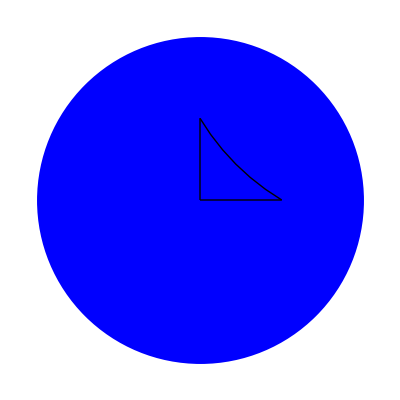

```mathematica
(*Vediamo un contraesempio con i vertici del triangolo rettangolo {{0,0},{0.5,0},{0,0.5}}*)
geodeticheNPunti[{{0,0},{0.5,0},{0,0.5}}]
```

```mathematica
(*Calcoliamo i valori dei cateti e la ipotenusa e verifichiamo che a^2!=b^2+c^2 *)
a=d[{0,0.5},{0.5,0}]
b=d[{0,0.5},{0,0}]
c=d[{0,0},{0.5,0}]
a^2==b^2+c^2
```

0.84035

0.549306

0.549306

False

#### 2.2. Somma degli angoli interni ad un triangolo

La somma degli angoli interni di un triangolo somma sempre meno di 180 gradi. Si può facilmente vedere che in un triangolo ci saranno al massimo due geodetiche-diametro. Pertanto vi sarà almeno un geodetica-cerchio. Vedendo come sono le geodetiche-cerchio, puoi immaginare che l’angolo diminuirà rispetto a se fosse geodetica-diametro. Abbiamo creato un Manipulate con 3 Locator per modificare il triangolo e vedere come variano gli angoli, senza mai superare la somma di 180 gradi. D’altra parte, sebbene non sia l’obiettivo principale di questo lavoro, è necessario ricordare che, nella geometria ellittica, la somma degli angoli di un triangolo supera sempre i 180 gradi. Questa è un’altra geometria non euclidea come l’iperbolica.

```mathematica
(*Calcola gli angoli di un triangolo*)
angoliTriangolo[P1_, P2_, P3_]:=Module[{tol,c,r,ang, ang1,ang2,ang3,vtg1,vtg2,vtg3,vtg4,vtg5,vtg6,somma},
tol=10^-5;
If[Det[{P1,P2}]!=0,                                               
c=centro[P1,P2];
r=radio[P1,P2];
ang=angolo[{P1[[1]]-c[[1]],P1[[2]]-c[[2]]},{P2[[1]]-c[[1]],P2[[2]]-c[[2]]}][[1]];
If[EuclideanDistance[{c[[1]]+r*Cos[ang], c[[2]]+r*Sin[ang]},P1]<tol,
vtg1={P1[[2]]-c[[2]],-(P1[[1]]-c[[1]])};
vtg3={-(P2[[2]]-c[[2]]),P2[[1]]-c[[1]]};
,(*else*)
vtg1={-(P1[[2]]-c[[2]]),P1[[1]]-c[[1]]};
vtg3={P2[[2]]-c[[2]],-(P2[[1]]-c[[1]])};
];
,(*else*)
vtg1={P1[[1]]-P2[[1]],P1[[2]]-P2[[2]]};
vtg3={P2[[1]]-P1[[1]],P2[[2]]-P1[[2]]};
];
If[Det[{P2,P3}]!=0, 
c=centro[P2,P3];
r=radio[P2,P3];
ang=angolo[{P2[[1]]-c[[1]],P2[[2]]-c[[2]]},{P3[[1]]-c[[1]],P3[[2]]-c[[2]]}][[1]];
If[EuclideanDistance[{c[[1]]+r*Cos[ang], c[[2]]+r*Sin[ang]},P2]<tol,
vtg4={P2[[2]]-c[[2]],-(P2[[1]]-c[[1]])};
vtg6={-(P3[[2]]-c[[2]]),P3[[1]]-c[[1]]};
,(*else*)
vtg4={-(P2[[2]]-c[[2]]),P2[[1]]-c[[1]]};
vtg6={P3[[2]]-c[[2]],-(P3[[1]]-c[[1]])};
];
,(*else*)
vtg4={P2[[1]]-P3[[1]],P2[[2]]-P3[[2]]};
vtg6={P3[[1]]-P2[[1]],P3[[2]]-P2[[2]]};
];
If[Det[{P1,P3}]!=0, 
c=centro[P1,P3];
r=radio[P1,P3];
ang=angolo[{P1[[1]]-c[[1]],P1[[2]]-c[[2]]},{P3[[1]]-c[[1]],P3[[2]]-c[[2]]}][[1]];
If[EuclideanDistance[{c[[1]]+r*Cos[ang], c[[2]]+r*Sin[ang]},P3]<tol,
vtg2={-(P1[[2]]-c[[2]]),P1[[1]]-c[[1]]};
vtg5={P3[[2]]-c[[2]],-(P3[[1]]-c[[1]])};
,(*else*)
vtg2={P1[[2]]-c[[2]],-(P1[[1]]-c[[1]])};
vtg5={-(P3[[2]]-c[[2]]),P3[[1]]-c[[1]]};
];
,(*else*)
vtg2={P1[[1]]-P3[[1]],P1[[2]]-P3[[2]]};
vtg5={P3[[1]]-P1[[1]],P3[[2]]-P1[[2]]};
];
ang1=VectorAngle[vtg1,vtg2]*(180/Pi);
ang2=VectorAngle[vtg3,vtg4]*(180/Pi);
ang3=VectorAngle[vtg5,vtg6]*(180/Pi);
somma=ang1+ang2+ang3;
{ang1,ang2,ang3,somma}
]

(*Per manipolare con il Locatore e vedere i angoli a lo stesso tempo*)
Manipulate[
Module[{angoli},
angoli=angoliTriangolo[punto1,punto2,punto3];
Column[{
geodeticheNPunti[{punto1,punto2,punto3}],
Row[{"Angolo 1: ",angoli[[1]]}],
Row[{"Angolo 2: ",angoli[[2]]}],
Row[{"Angolo 3: ",angoli[[3]]}],
Row[{"Somma di angoli: ",angoli[[4]]}]
}]
],
{{punto1,{-0.5,-0.5}},Locator},
{{punto2,{0.5,0.5}},Locator},
{{punto3,{0.25,-0.25}},Locator}
]
```

### 3. Quinto postulato dei paralleli di Euclide

Il quinto postulato di Euclide dice que se una retta taglia altre due rette determinando dallo stesso lato angoli interni la cui somma è minore di quella di due angoli retti, prolungando indefinitamente le due rette, esse si incontreranno dalla parte dove la somma dei due angoli è minore di due angoli retti. Ciò equivale a dire che dati una qualsiasi retta r e un punto P non appartenente a essa, è possibile tracciare per P una e una sola retta parallela alla retta r data.
Sappiamo che la geometria iperbolica è ottenuta rimpiazzando il postulato delle parallele con il cosiddetto postulato iperbolico, nel modo seguente:
Per un punto esterno a una retta data passano almeno due rette parallele. 
Verifichiamolo con mathematica!

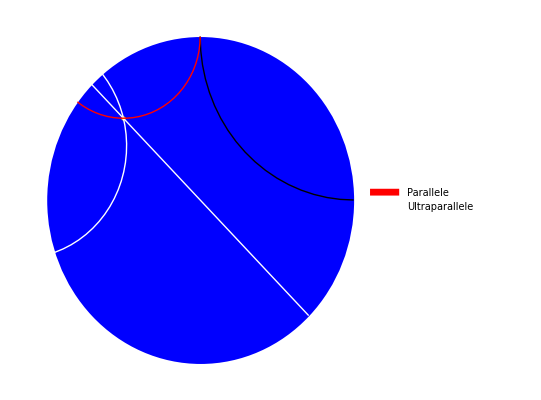

```mathematica
gr={ Black,Thick,geodeticaArco[{1,0},{0,1}],White,geodeticaDiametro[{-0.5,0.5},{0.5,-0.5}],geodeticaArco[{-0.5,0.5},{-0.8,-0.25}],Red,geodeticaArco[{-0.5,0.5},{0,1}]};

geodetica5Postulado=
Graphics[{Blue, Disk[],Yellow,PointSize->Large,Point[{-0.5,0.5}],gr, PlotRange->{{-1,1},{-1,1}}},PlotRangePadding->Scaled[0.07]];

Legended[geodetica5Postulado,Placed[SwatchLegend[{Red,White},{"Parallele","Ultraparallele"}],{Right,Top}]]
```

Inoltre, ci sono infinite rette parallele che non intersecano la retta nera e passano per il punto che abbiamo preso. Noi abbiamo disegnato una retta rossa, che interseca la nera solo nel bordo del disco. Quando due rette verificano questo le chiamamo rette parallele. Però alle rette verdi, che non intersecano mai la retta nera, le chiamamo rette ultraparallele della nera. Questi sono due concetti comunemente conosciuti.

### 4. Forma di un cerchio

Abbiamo creato un’altro Manipulate per vedere la forma dei cerchi nel disco di Poincaré.

```mathematica
(*Funzione per creare un cerchio, dato il centro e il ratio, formato dai punti che si trovano a distanza r del centro nella geometria iperbolica*)
PoincareCerchio[c_,r_]:=Module[{disco},disco=RegionPlot[x^2+y^2<=1,{x,-1,1},{y,-1,1},PlotStyle->Directive[LightBlue,Opacity[0.5]]];
ContourPlot[d[c,{x,y}]==r,{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},x^2+y^2<=1],Epilog->{Red,PointSize[Large],Point[c]},PlotPoints->3,MaxRecursion->3]//Show[#,disco]&];

(*Per manipolare con il Locator*)
Manipulate[PoincareCerchio[punto, 1],{{punto,{0.4,0.4}},Locator}]
```

### 5. Esistencia di tassellazioni con riflessioni

```mathematica
(*Funzione per riflettere un punto rispetto ad una geodetica*)
rifletta[P_,P1_,P2_]:=Module[{z0,z1,z2,z,α,c,eq1,eq2,inters},
z1=P1[[1]]+P1[[2]]*I;
z2=P2[[1]]+P2[[2]]*I;
z0=P[[1]]+P[[2]]*I;
If[Det[{P1,P2}]==0,
	If[P1!={0,0}, eq1=P1[[2]]*x==P1[[1]]*y, eq1=P2[[2]]*x==P2[[1]]*y];
	eq2=x^2+y^2==1;
	inters=NSolve[{eq1,eq2},{x,y}];
	α=(x/.inters[[1]])+(y/.inters[[1]])*I;
	z=α^2*Conjugate[z0]//N;
,(*else*)
	c=centro[P1,P2];
	α=c[[1]]+c[[2]]*I;	
	z=(α*Conjugate[z0]-1)/(Conjugate[z0]-Conjugate[α])//N;
];
{P1,{Re[z],Im[z]}}]

(*Rifletta un punto rispetto ad un insieme di geodetiche*)
riflettaGeodetiche[P_,punti_]:=Module[{nuoviPunti, N,riflessione},
nuoviPunti={};
N=Length[punti];
Do[
riflessione=rifletta[P,punti[[i]],punti[[i+1]]];
nuoviPunti=Join[nuoviPunti, riflessione];
,{i,1,N-1}];
nuoviPunti=Join[nuoviPunti, {punti[[N]]}];
nuoviPunti
]

(*Disegna la tassellazione iterando le reflessioni*)
tassellazione[nit_,triangoloIniziale_]:=Module[{P,geodetiche,poligonoDisegno},
P={triangoloIniziale[[1]],triangoloIniziale[[2]],triangoloIniziale[[3]]};
geodetiche={{P[[2]],P[[3]]},{P[[3]],P[[1]]},{P[[1]],P[[2]]}};
poligonoDisegno=Join[triangoloIniziale,{P[[1]]}];
Do[
Do[geodetiche[[i]]=riflettaGeodetiche[P[[i]],geodetiche[[i]]],{i,1,3}];

poligonoDisegno=Join[poligonoDisegno,Rest[geodetiche[[3]]], Rest[geodetiche[[1]]],Rest[geodetiche[[2]]]];
,nit];

geodeticheNPunti[poligonoDisegno]]
```

Prima tassellazione:

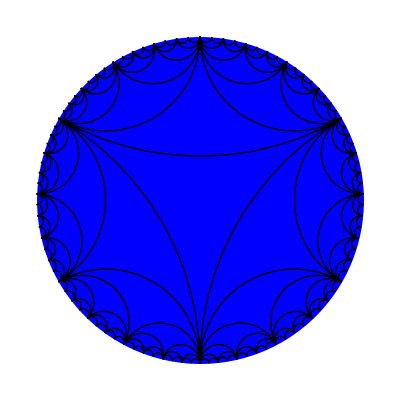

```mathematica
tassellazione[5,{{0,-1},{(√3)/2,1/2},{-(√3)/2,1/2}}]
```

Seconda  tassellazione:

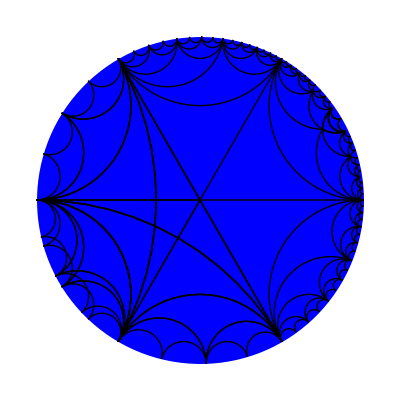

```mathematica
tassellazione[5,{{0,0},{1,0},{Cos[Pi/3],Sin[Pi/3]}}]
```

### 6. Curiosità extra

Abbiamo scoperto che si può calcolare il centro con tecniche di riga e compasse:
1-Uniamo P1 con l’origine e lo chiamiamo r1.
2-Disegniamo la perpendicolare a r1 passando per P1 e scegliamo uno dei punti di intersezione con la circonferenza unitaria.Chiamiamo questo punto perp1.
3-Uniamo perp1 con l’origine e lo chiamiamo r2.
4-Costruiamo la perpendicolare a r2 che è tangente al cerchio. Chiameremo il punto di intersezione di questa linea con r1 inv1.
5-Prendiamo 2 mediatrici dal triangolo P1,P2,inv1 e dove si intersecano è il centro c.

```mathematica
perp1[P1_]:=NSolve[{x^2+y^2==1,P1[[1]](x-P1[[1]])==-P1[[2]](y-P1[[2]])},{x,y}][[1]]
inv1[P1_]:=NSolve[{(x/.perp1[P1])(x-(x/.perp1[P1]))+(y/.perp1[P1])(y-(y/.perp1[P1]))==0, P1[[2]]*x==P1[[1]]*y},{x,y}][[1]]

mediatr[P1_,P2_]:=(P2[[1]]-P1[[1]])*(x-(P1[[1]]+P2[[1]])/2)+(P2[[2]]-P1[[2]])*(y-(P1[[2]]+P2[[2]])/2)==0

centroTechnicalDrawing[P1_,P2_]:=Module[{eq1,eq2,c},
eq1=mediatr[P1,P2];
eq2= mediatr[P1,{(x/.inv1[P1]),(y/.inv1[P1])}];
 c = NSolve[{eq1,eq2},{x,y}][[1]];
{c[[1,2]],c[[2,2]]}]

(*Definir la función graficoCentri*)graficoCentri[P1_,P2_]:=Graphics[{Green,Disk[],Yellow,PointSize->Large,Point[P1],Point[P2],Blue,PointSize->0.025,Point[centroTechnicalDrawing[P1,P2]],Red,PointSize->0.015,Point[centro[P1,P2]]}]

(*Usar Manipulate para crear el gráfico con leyenda*)
Manipulate[Legended[graficoCentri[punto1,punto2],Placed[SwatchLegend[{Red,Blue},{"Centro","Centro riga e compasse"}],{Right,Top}]],{{punto1,{0.5,0.25}},Locator},{{punto2,{0.5,-0.25}},Locator}]
```